```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
e = Import["evol.dat"];
```

```mathematica
b=Transpose[e][[2]];
a=Transpose[e][[3]];
```

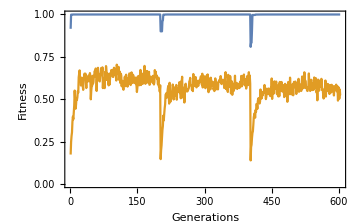

```mathematica
ListLinePlot[{b,a},PlotRange->All,Frame->True,FrameLabel->{"Generations","Fitness"},ImageSize->Medium]
```

```mathematica
n  = Transpose[Import["neural.dat"]];
w  = Transpose[Import["weights.dat"]];
b = Transpose[Import["biases.dat"]];
```

```mathematica
t = Table[x,{x,0.01,100,0.01}];
```

```mathematica
n=Table[Transpose[{t,n[[i]]}],{i,1,Length[n]}];
w=Table[Transpose[{t,w[[i]]}],{i,1,Length[w]}];
b=Table[Transpose[{t,b[[i]]}],{i,1,Length[b]}];
```

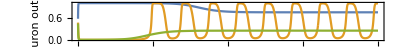

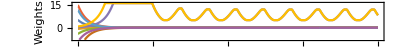

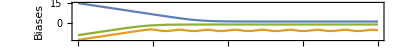

```mathematica
ListLinePlot[n,AspectRatio->1/10,ImageSize->Full,Frame->True,FrameLabel->{"Time","Neuron output"}]
ListLinePlot[w,AspectRatio->1/10,ImageSize->Full,Frame->True,FrameLabel->{"Time","Weights"}]
ListLinePlot[b,AspectRatio->1/10,ImageSize->Full,Frame->True,FrameLabel->{"Time","Biases"}]
```